## Subtitle. Reference Distributions

## Section. Introduction

Box, Hunter, and Hunter (1978) use the terms "reference set" and "reference distribution" to explain the concept of hypothesis testing or significance testing.  We will see that sampling distributions of sample statistics are commonly used as reference distributions when certain assumptions are valid.  Essentially, a "reference distribution" is a relative frequency distribtion that we may use to weigh the strength of competing hypotheses.  Frequently, the competing hypotheses are of the form "the treatment had no effect vs. the treatment had an effect".  The hypothesis,  "the treatment had no effect" is called the null hypothsis and sometimes denoted H_o.  The statement "the treatment had an effect" is called the alternative hypothesis, H_a or H_1.  Here, the term "treatment" refers to any intervention, for example a new drug or therapy treating some disease, a new procedure for improving a manufacturing process, an alternative method for issuing credit cards, or as in the example to follow, a particular method to choose employees.

## Section. Employment Discrimination

In the early 1990's in an effort to reduce the New York State budget, Governor Mario Cuomo called for an across the board reduction in the New York State Government work force.  As a result, the management administration unit of one of the agencies was required to lay off eleven individuals, approximately nine percent of their 127 employees.  Three of the eleven laid off employees were over fifty years old and filed an age discrimination suite in Federal District Court.  As a first step in their argument, they noted that the average age of those laid off was greater than that of those retained.  An argument such as this is required of the plaintiff to shift the burden of proof from the plaintiff to the defendant.

In such cases there is an initial burden on the plaintiff to show that there was disparate impact on the protected class; this is usually accomplished by a statistical test of the hypothesis of no disparate impact. We may construct an experiment to introduce the concept of hypothesis testing to the jury, and to decide if obtaining an average age at least as large as that of those laid off is a particularly unusual event.

The cell below defines lists of ages for those employees retained and laid off.  We need to determine if the plaintiff's claim that the average age of the two groups are different, and if so could such a difference have happened merely by chance.

```mathematica
notlisted={29,34,36,44,36,47,33,33,45,45,36,
		26,29,37,29,30,38,38,57,40,47,41,42,45,48,
		33,62,43,44,32,40,32,25,47,36,31,24,50,26,
		42,45,32,46,28,42,53,45,57,26,62,46,49,47,
		31,40,42,28,45,30,53,27,48,29,40,48,47,42,
		44,36,66,40,40,47,38,29,31,37,39,47,42,58,
		60,52,48,43,47,37,39,21,41,31,39,39,53,41,
		25,48,51,41,23,48,48,62,66,44,48,35,45,37,
		46,34,40,33,32,40,30};
layofflist={42,39,37,57,33,42,60,39,56,44,28};
```

First we obtain the average age of employees who were retained and of those laid off and the lengths of the respective lists.

```mathematica
Mean[notlisted]//N
```

40.6983

```mathematica
Mean[layofflist]//N
```

43.3636

```mathematica
{Length[notlisted],Length[layofflist]}
```

{116,11}

The average age of those on the layoff list is clearly larger than the average age of those retained, but could a difference of this magnitude have been a result of chance.  One approach to answering this question is to construct a reference distribution for the statistic of interest, i.e. the mean age of eleven randomly chosen people from a list of 127.  The cell below creates a list of the ages of the employees prior to the lay off by joining the layoff and retained lists.  There are (127!)/((127-11)!)possible eleven person layoff lists that could have been created from the 127 individuals employed by this unit prior to the reduction in force.  The list of these (127!)/((127-11)!)average ages we be a proper reference distribution for the statistic in question, but this would be an extremely long list to construct and we may be able to answer our question with somewhat less work.  To approximate the proper reference distribution, consider creating several randomly generated layoff lists, finding the means of these lists, and finding the proportion of these lists with means larger than 43.3636,  the mean of the actual layoff list.

```mathematica
mgtadmin=Join[layofflist,notlisted];
```

```mathematica
Length[mgtadmin]
```

127

The command below will select a random sample of size 11 from the ages in mgtadmin.

```mathematica
RandomSample[mgtadmin,11]
```

{51,60,62,39,27,45,42,66,42,34,40}

Here we generate 100 lists of length 11 from the ages in the list "mgtadmin", and then find the means of these 100 randomly chosen lay off lists.

```mathematica
randomlists=Table[RandomSample[mgtadmin,11],{100}];
```

```mathematica
means=Table[N[Mean[randomlists⟦i⟧]],{i,1,100}];
```

How many of these means are below and above the mean of the actual lay off list, 43.3636.  Are the ages that we have observed in the lay off list rare?

```mathematica
BinCounts[means,{{0,43.36,100}}]
```

{82,18}

We may visualize the distribution of the means of the randomly chosen lay off lists.  We may consider this distribution an approximation of the reference distribution of interest, i.e. the distribution of the means of all possible lay off lists of length 11 chosen from the 127 ages of the employees of the unit, which we may also call the sampling distribution of the sample mean for samples of size 11.

```mathematica
f=BinCounts[means,{29.5,50.5,1}]
```

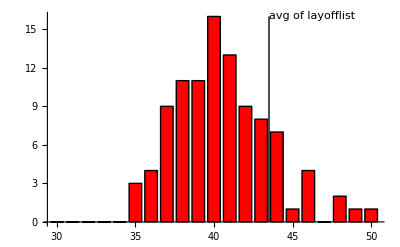

```mathematica
BarChart[f,PlotRange->{0,Max[f]},BarLabels->Table[i,{i,30,50}],Axes->True,Epilog->{Text["avg of layofflist",{14.5,Max[f]},{-1,0}],Line[{{14.5,0},{14.5,Max[f]}}]}]
```

By generating 100 random layoff lists we get an idea of the likelihood of randomly picking a list with an average age equal to or greater than that of the plaintifs (43.36). Here, the proportion of times that the average age of a randomly choosen list exceeded 43.36 was not rare enough for the jury to conclude disparate impact. Inasmuch as the plaintiffs’ lawyers failed to meet this burden of proof, much of their remaining evidence was irrelevant.

Actually, the evidence proposed by plaintiff's attorney was not appropriate.  In age disrimination cases, the protected class is those over 40 years of age.  The fact that the average age of those laid off was larger than the average age of those retained is technically irrelevant.  Ordinarily, in disrimination cases the plaintiff will construct a 2×2 table displaying the numbers of individuals (laid off or retained) by (protected or not), and then attempt to argue that an unusually disproportionate number of the protected class was treated unfairly.  Using the hypergeometric distribution, one may calculate the probability of randomly observing the table in question or one more extreme (i.e., more damaging to the protected class), given that the marginal counts are held constant (e.g., 55 less than 40 years of age and 72 older, 11 listed for layoff, while 116 were not).  If the sum of these probabilities is small, we reject the hypothesis of no disparate impact. This is called Fisher’s exact test. By observing the table for our age discrimination case (see below), it is clear that a lesser proportion of the protected class was listed for layoff than that proportion of the unprotected class. Here there is no need to calculate probabilities, since it is clear that there is a greater proportion of people over 40 in the group not laid off than there is in the laid off group.

| <40 | ≥40 | Total
laid off | 5 | 6 | 11
not laid off | 50 | 66 | 116
Total | OverBar[55] | OverBar[72] | OverBar[127]

### An Hypothesis Testing Lab Activity

Scheaffer, et.al., (1995) describe a number of discrimination cases that lend themselves to analysis using randomization tests.  For example, in a 1977 racial discrimination case, Dendy v. Washington Hospital Center, four of nine African-American nurses passed an examination while all 26 white nurses passed.  In other words, five nurses failed the exam and they were all from the protected class.  In cases of this type, it may be argued that employment tests are discriminatory if they adversely impact a protected class.  In order to be successful the plaintiff endeavors to shift the burden of proof to the defendant by using statistical evidence to reject the null hypothesis that the impact on the protected class is the same as that on the unprotected class.  If the plaintiff is successful in establishing this disparate impact, then the defendant must prove that the use of such criteria is a business necessity.

In this example, the reference set consists of all possible lists of five nurses from the 35 nurses who took the exam.  There are (35 34 33 32 31) or 38,955,840 such lists.  If we ignore the ordering in the list there are only (35
5) or 324,632 possible lists of length five.  We could have the computer list them and count how many times the list contained only Black nurses.  Or, as above, we could approximate this reference distribution by taking a large sample from it and find the relative frequency of the event that we observed (five Black nurses, no white nurses) plus the relative frequencies of any more extreme events (there are none).

With an ordinary deck of playing cards we may develop an approximate reference distribution for assessing the likelihood of the observed event, i.e. four of nine African-American nurses passed an examination while all 26 white nurses passed.  If we discard 17 black cards from the deck and shuffle it thoroughly, we may deal five cards representing one realization of this examination situation were success on the exam is unrelated to race.  If we repeat this experiment a large number of times we may assess the likelihood that all five failures are from the nine nurses belonging to the protected class.

Of course, we could have avoided experimentation by applying our knowledge of the hypergeometric distribution from our study of discrete probability distributions. Here we need only calculate this single probability since there is no more extreme outcome than the observed one, given the marginal totals.

Binomial[35, 5] is a Mathematica function calculating the combination of 53 things taken 5 at a time, i.e., 35 choose 5.

```mathematica
Binomial[35,5]
```

```mathematica
PDF[HypergeometricDistribution[5,9,35],5]//N
```

```mathematica
(Binomial[9,5] Binomial[26,0])/Binomial[35,5]
```

```mathematica
%//N
```

```mathematica
fHypGeo=Table[PDF[HypergeometricDistribution[5,9,35],x],{x,0,5}]//N
```

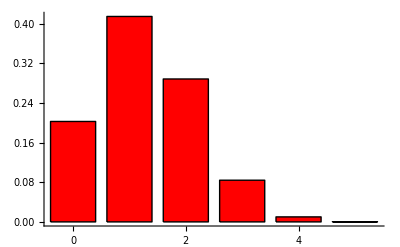

```mathematica
BarChart[fHypGeo,PlotRange->{0,Max[fHypGeo]},BarLabels->Table[i,{i,0,5}],Axes->True]
```

## Section. Sampling Distributions

Suppose that a very large number of random samples, all of size n, are drwan from some population of measurements.  These samples are depicted in column 2 of the following table.  Now, for each of these very large number of samples, we may calculate any sample statistic, e.g. Ȳ, S^2, the range, ((n-1)S^2)/σ^2, the median, some arbitrary variable W.  Now let's consider any one of these, say the range.  We have depicted this large number of ranges in column 5 of the table below.  Think of constructing a relative frequency distribution of these very large number of ranges.  This we will call the sampling distribution of the Range.

RV's | (Y_1,Y_2,Y_3,...,Y_n) | Ȳ | S^2 | Range | ((n-1)S^2)/σ^2 | Median | W
sample 1 | (y_1,y_2,y_3,...,y_n)_1 | (ȳ)_1 | (s^2)_1 | (range)_1 | (((n-1)s^2)/σ^2)_1 | (median)_1 | (w)_1
sample 2 | (y_1,y_2,y_3,...,y_n)_2 | (ȳ)_2 | (s^2)_2 | (range)_2 | (((n-1)s^2)/σ^2)_2 | (median)_2 | (w)_2
sample 3 | (y_1,y_2,y_3,...,y_n)_3 | (ȳ)_3 | (s^2)_3 | (range)_3 | (((n-1)s^2)/σ^2)_3 | (median)_3 | (w)_3
 |  |  |  | □ | □ | □ | □
sample ∞ | (y_1,y_2,y_3,...,y_n)_∞ | (ȳ)_∞ | (s^2)_∞ | (range)_∞ | (((n-1)s^2)/σ^2)_∞ | (median)_∞ | (w)_∞

### Section.Subsection. A Quality Control Example

Hildebrand and Ott (1998) describe an example where a meat packer has installed a new meat cutting process.  This process is suppose to produce steaks whose average weight is 12 ounces.  From the statement that no steaks should weigh less than 11.5 ounces, nor more than 12.6 ounces, we get the idea that the range of weights should be about 1.1 ounces and therefore the standard deviation, s, would be in the neighborhood of 1.1/6≐ 0.2.  The meat packer proposes selecting a random sample of ten steaks each week and weighing them to monitor the process.  The information in each weeks sample needs to be summarized.  At least two summary measures could be useful, a measure of location (e.g. mean or median) and a measure of dispersion (e.g. range, variance, standard deviation, interquartile range).  Suppose each week we calculate the mean, x̄, and the variance, s^2.  How may we judge the current state of the process based on these measures.  Since we certainly do not expect that x̄ will always be 12 and that s^2 will always be 0.2, we need some way to guage if the observed values of x̄  and s^2 are at all unusual.  For each measure, we need to refer to some relative frequency distribution of that statistic.  In as much as we do not have a long history of these samples to which we may refer, we must make a few assumptions and infer what the appropriate reference distributions, i.e. sampling distributions, look like.

#### Section.Subsection.Subsubsection. Means

If we assume that the weight of the steaks follow a normal or Gaussian distribution (and there are some good reasons to suspect this is true) then the sampling distribution of x̄ will also be normal.  From what we know about means and variances of linear combinations or random variables, the mean of the distribution of x̄ 's is the mean of the population from which the sample was drawn, μ, which in this example is 12 if the process is working as expected.  And the variance of the distribution of the x̄ 's is the variance of the population from which the sample was drawn divided by the sample size, σ^2/n, here 0.2^2/10or 0.004.  Thus the standard deviation of the sampling distribution of x̄ is σ/(√n), here 0.2/(√10)≐0.063.  Now, by comparing any observed x̄ with the quantiles of the normal distribution with mean 12 and standard deviation 0.063, we may decide if we have observed something unusual.  This is essentially an hypothesis test and if we make a graphical representation of these weekly tests, we have a control chart, in this case an x̄ chart, one of the quality control charts originally proposed by Shewart.

Let's see how this works.  First we will generate many samples of size 10 from our process with mean 12 and standard deviation 0.2.  Calculating the mean of each sample we may draw an approximation to the sampling distribution of x̄.

Before we do this, lets run through our experiment with smaller numbers.  Below we will generate the weights of steaks for three samples each sample of size 5.  We may think of this as samples of size five randomly selected from the cutting process during three distinct weeks.

```mathematica
steakSamples=Table[Random[NormalDistribution[12,0.2]],{indexForSamples,1,3},{indexWithinSample,1,5}]
```

{{11.9859,12.1461,12.1491,11.7662,11.5259},{11.9819,12.125,12.0758,11.8769,11.9211},{12.1009,11.9973,12.0116,11.9252,11.8366}}

We now calculate the mean weight for each of the three weeks.  We notice that none of these three means is exactly 12 and there are means both below and above 12.

```mathematica
steakSamplesMeans= Table[Mean[steakSamples⟦i⟧ ],{i,1,Length[steakSamples]}]
```

{11.9146,11.9961,11.9743}

We now replace the three samples above with a more ambitious 500 samples, this time all of size ten.  We do not want to print this 500 by 10 table, so we suppress the printing by ending are input with a semi-colon.  Next we find the mean of each of the 500 samples of size ten, and then we find the mean and standard deviation of the 500 means.  We expect the mean of the x̄'s to be near μ=12 , and the standard deviation of the x̄'s to be in the neighborhood of σ/(√n)≐0.063.

```mathematica
steakSamples=Table[Random[NormalDistribution[12,0.2]],{indexForSamples,1,500},{indexWithinSample,1,10}];
```

```mathematica
steakSamplesMeans= Table[Mean[steakSamples⟦i⟧ ],{i,1,Length[steakSamples]}];
```

```mathematica
Sort[steakSamplesMeans]
```

```mathematica
{Sort[steakSamplesMeans][[13]],Sort[steakSamplesMeans][[487]]}
```

{11.8854,12.1158}

```mathematica
{Mean[steakSamplesMeans],StandardDeviation[steakSamplesMeans]}
```

{12.0035,0.0597094}

The relative frequency polygon of the x̄'s appears to unimodal and symmetric, reminiscent of a bell shaped normal curve.

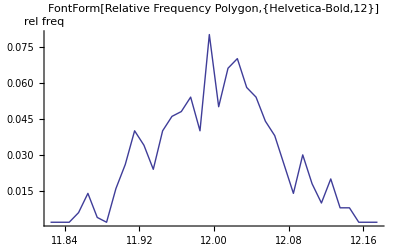

```mathematica
relFreqPolygon[steakSamplesMeans,Table[xbars,{xbars,12-3 (.06),12+ 3 (.06),.01}]]
```

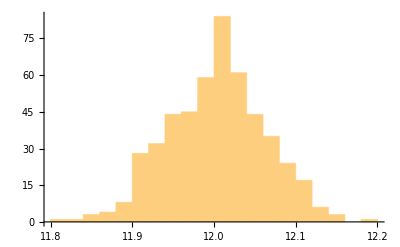

```mathematica
Histogram[steakSamplesMeans]
```

Suppose we list and plot the first twenty x̄'s.  Are any of the unusual?  We know from the empiical rule that 95% of the x̄'s should be within two of their standard deviations of their mean, in other words between μ-2 σ/(√n)and μ+2 σ/(√n), e.g. between 12-2 0.2/(√10)and 12+2 0.2/(√10), or between 11.8735 and 12.1265.

```mathematica
Take[steakSamplesMeans,20]
```

{12.0324,11.9559,12.0151,12.0597,12.0386,12.0618,11.9508,11.994,12.1434,11.9189,12.0176,11.8988,11.9217,11.9657,11.9874,12.0868,11.9998,11.9695,12.0459,11.8206}

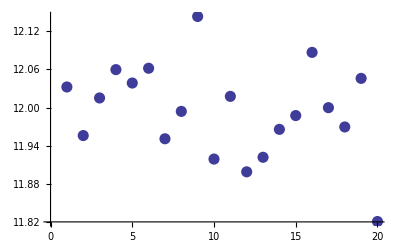

```mathematica
ListPlot[Take[steakSamplesMeans,20],PlotStyle->PointSize[0.02],PlotStyle->PointSize[0.02]]
```

```mathematica
BinCounts[Take[steakSamplesMeans,20],{{0,11.8735,12.1265,100}}]
```

{1,19,0}

Nothing appears to be unusual.

#### Section.Subsection.Subsubsection. Variances

```mathematica
steakSamplesVars= Table[Variance[steakSamples⟦i⟧ ],{i,1,Length[steakSamples]}]
```

```mathematica
steakSamplesSDs= Table[StandardDeviation[steakSamples⟦i⟧ ],{i,1,Length[steakSamples]}]
```

```mathematica
Sort[steakSamplesSDs]
```

```mathematica
Sort[steakSamplesSDs][[0.95 Length[steakSamples]]]
```

0.269416

```mathematica
{Mean[steakSamplesVars],StandardDeviation[steakSamplesVars]}
```

{0.0403125,0.0182494}

The relative frequency polygon of the s^2's does not appear to be symmetric. It is skewed to the right.  Actually it is the shaped like a χ^2 distribution, but the scale is not quite correct.  The statistic ((n-1)s^2)/σ^2 has a χ^2 distribution with (n-1) degrees of freedom, i.e χ_(n-1)^2 or here χ_9^2.  We would expect ((n-1)s^2)/σ^2(which in this case is (9 s^2)/0.2^2) to exceed the 95^th percentile of χ_(n-1)^2 much more than 5% of the time.  The 95^th percentile of χ_9^2 is 16.919, i.e.  χ_(9, 0.95)^2=16.919.

```mathematica
Quantile[ChiSquareDistribution[9],0.95]
```

16.919

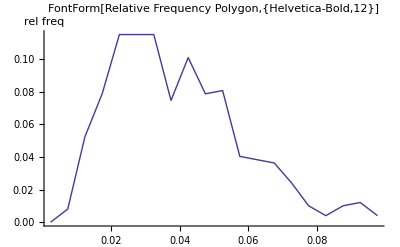

```mathematica
relFreqPolygon[steakSamplesVars,Table[var,{var,0,0.1,.005}]]
```

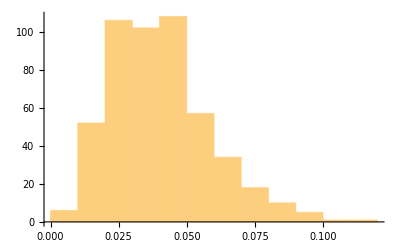

```mathematica
Histogram[steakSamplesVars]
```

```mathematica
(9(Take[steakSamplesVars,20]))/0.2^2
```

{4.02758,11.4028,9.41788,8.12939,9.66734,5.6742,5.8346,8.35678,5.89167,6.44549,6.40906,14.1642,5.40129,6.85377,7.06726,10.2529,3.43556,3.55065,7.7724,7.58985}

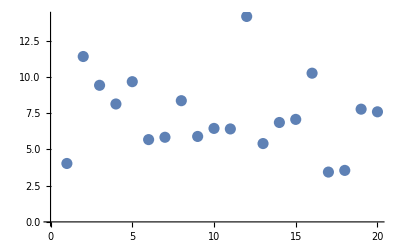

```mathematica
ListPlot[(9 Take[steakSamplesVars,20])/0.2^2,PlotStyle->PointSize[0.02],PlotStyle->PointSize[0.02]]
```

```mathematica
BinCounts[(9 Take[steakSamplesVars,20])/0.2^2,{{0,16.919,100}}]
```

{20,0}

If we want to construct a control chart for s^2, we need only to rewrite the following inequality with s^2 on the right side.  The sample variance is unusual if ((n-1)s^2)/σ^2>χ_(9, 0.95)^2, or s^2>(σ^2  χ_(9, 0.95)^2)/(n-1), or s>√((σ^2  χ_(9, 0.95)^2)/(n-1)).

```mathematica
√((0.2^2  16.919)/(10-1))
```

0.274218

## Section. References

Box, G.E.P., W.G. Hunter, and J.S. Hunter (1978), Statistics for Experimenters,  Wiley, New York.

Hildebrand, D.H. and R.L. Ott (1998), Statistical Thinking for Managers, Brooks/Cole, Pacific Grove, CA.

Scheaffer, R.L., A. Watkins, M. Gnanadesikan, and J. Witmer, 1995, Activity-Based Statistics, National Science Foundation, Grant No. USE-9150836.

## Section. Some Descriptive Statsitics Functions

```mathematica
Needs["Statistics`"];
Needs["VisualStats`"];
Needs["Graphics`"];
Needs["Combinatorica`"];
```

Get::noopen: Cannot open "Statistics`".

Needs::nocont: Context "Statistics`" was not created when Needs was evaluated.

Get::noopen: Cannot open "VisualStats`".

Needs::nocont: Context "VisualStats`" was not created when Needs was evaluated.

Get::noopen: Cannot open "Graphics`".

Needs::nocont: Context "Graphics`" was not created when Needs was evaluated.

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

```mathematica
relFreqPolygon[dataArray_,extendedBoundries_]:=ListPlot[Transpose[{classMidPoints[extendedBoundries],relFreqs[dataArray,extendedBoundries]}],Joined->True,PlotRange->All,PlotLabel->FontForm["Relative Frequency Polygon",{"Helvetica-Bold",12}],AxesLabel->{" ","rel\nfreq"},AxesOrigin->{Min[extendedBoundries],0}]
```

```mathematica
relFreqPolygon[dow30Prices,pricesExtendedClassBoundries];
```

```mathematica
cumRelFreqGraph[dataArray_,extendedBoundries_]:=ListPlot[Transpose[{upperBoundry[extendedBoundries],relCumFreqs[dataArray,extendedBoundries]}],Joined->True,PlotRange->All,PlotLabel->FontForm["Cumulative Relative\n   Frequency Graph",{"Helvetica-Bold",12}],FrameLabel->{"y","cum rel freq",None,None},GridLines->Automatic,Frame->True]
```

```mathematica
cumRelFreqGraph[dow30Prices,pricesExtendedClassBoundries];
```

### Some Descriptive Statistics Functions

```mathematica
classes[boundries_]:=Table[{boundries⟦i⟧,boundries⟦i+1⟧},{i,1,Length[boundries]-1}];
lowerBoundry[boundries_]:=Transpose[classes[boundries]]⟦1⟧;
upperBoundry[boundries_]:=Transpose[classes[boundries]]⟦2⟧;
classMidPoints[boundries_]:=1/2 Plus@@Transpose[Table[{boundries⟦i⟧,boundries⟦i+1⟧},{i,1,Length[boundries]-1}]];
classFreqs[dataArray_,boundries_]:=Drop[Drop[RangeCounts[dataArray,boundries],1],-1];
relFreqs[dataArray_,boundries_]:=N[classFreqs[dataArray,boundries]/(Plus@@classFreqs[dataArray,boundries]),2];
cumFreqs[dataArray_,boundries_]:=Accumulate[classFreqs[dataArray,boundries]];
relCumFreqs[dataArray_,boundries_]:=N[Accumulate[classFreqs[dataArray,boundries]]/(Plus@@classFreqs[dataArray,boundries]),2];
freqTable[dataArray_,boundries_]:=Transpose[{lowerBoundry[boundries],upperBoundry[boundries],classMidPoints[boundries],classFreqs[dataArray,boundries],relFreqs[dataArray,boundries],cumFreqs[dataArray,boundries],relCumFreqs[dataArray,boundries]}]
```

## Section. Dice

The command below will select a random integer between 1 and 6

```mathematica
RandomInteger[{1,6}]
```

4

```mathematica
RandomInteger[{1,6},4]
```

{4,6,5,3}

```mathematica
RandomInteger[{1,6},{5,4}]
```

{{3,2,3,2},{4,2,4,6},{4,1,2,1},{3,5,4,2},{1,6,4,2}}

```mathematica
dicerolls=RandomInteger[{1,6},{5,4}]
```

{{4,1,2,3},{5,5,6,3},{1,2,3,2},{3,6,2,3},{4,5,1,3}}

```mathematica
means=Table[N[Mean[dicerolls⟦i⟧]],{i,1,5}]
```

{2.5,4.75,2.,3.5,3.25}

```mathematica
dicerolls=RandomInteger[{1,6},{1000,4}];
```

```mathematica
f=BinCounts[Flatten[dicerolls],{0.5,6.5,1}]
```

{658,666,657,672,657,690}

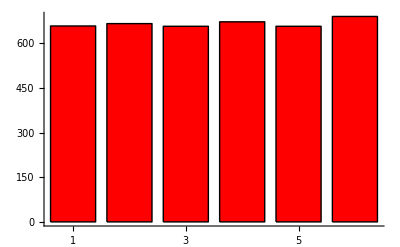

```mathematica
BarChart[f,PlotRange->{0,Max[f]},BarLabels->Table[i,{i,1,6}],
Axes->True]
```

```mathematica
means=Table[N[Mean[dicerolls⟦i⟧]],{i,1,1000}];
```

```mathematica
f=BinCounts[means,{1,6,.1}]
```

{1,0,4,0,0,8,0,8,0,0,25,0,51,0,0,65,0,92,0,0,89,0,101,0,0,111,0,103,0,0,83,0,82,0,0,62,0,51,0,0,27,0,21,0,0,12,0,3,0,0}

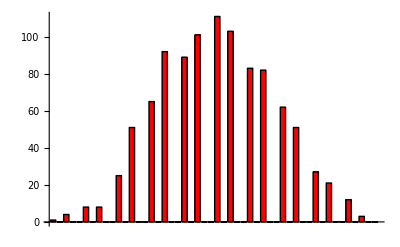

```mathematica
BarChart[f,PlotRange->{0,Max[f]},BarLabels->" ",Axes->True]
```

With 25 rolls.

```mathematica
dicerolls=RandomInteger[{1,6},{1000,25}];
```

```mathematica
means=Table[N[Mean[dicerolls⟦i⟧]],{i,1,1000}];
```

```mathematica
f=BinCounts[means,{1,6,.1}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,3,2,12,10,29,53,55,102,89,158,99,141,56,81,38,30,13,17,4,6,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0}

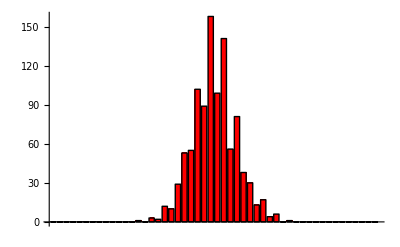

```mathematica
BarChart[f,PlotRange->{0,Max[f]},BarLabels->" ",Axes->True]
```

```mathematica
{Mean[means],StandardDeviation[means]}
```

## Section. Meat Packer

```mathematica
RandomArray[NormalDistribution[12,0.2], 10]
```

{11.9457,11.9569,11.7099,11.8782,12.0356,12.2649,11.6498,12.4402,11.796,12.0781}

```mathematica
Mean[RandomArray[NormalDistribution[12,0.2],10]]
```

12.0269

```mathematica
StandardDeviation[RandomArray[NormalDistribution[12,0.2],10]]
```

0.125599

```mathematica
randomWeeks=Table[RandomArray[NormalDistribution[12,0.2],10],{3}]
```

{{11.7253,12.0495,11.9982,12.0308,12.0274,12.1827,11.6785,11.9549,12.1854,12.322},{11.8863,11.8945,11.6897,11.858,12.0989,12.0562,12.0981,12.1969,12.0522,12.0741},{11.7749,12.3185,11.7289,12.0863,12.1027,11.899,12.1007,12.2612,11.7575,11.6662}}

```mathematica
randomWeeks=Table[RandomArray[NormalDistribution[12,0.2],10],{100}];
```

```mathematica
leftline=RandomArray[NormalDistribution[12,0.2],1000];
rightline=RandomArray[NormalDistribution[13,0.2],1000];
```

```mathematica
randomWeeksRight=Table[RandomArray[NormalDistribution[12,0.2],10],
{100}];
```

```mathematica
Histogram[{leftline,rightline}]
```

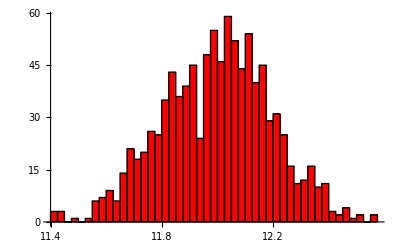

```mathematica
Histogram[RandomReal[NormalDistribution[12,0.2],1000]]
```

```mathematica
means=Table[Mean[RandomArray[NormalDistribution[12,0.2],10]],{i,1,3}]
```

{11.9475,11.9347,11.8549}

```mathematica
means=Table[Mean[RandomArray[NormalDistribution[12,0.2],10]],
{i,1,100}];
```

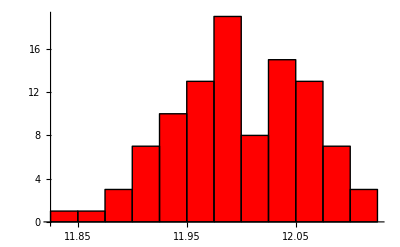

```mathematica
Histogram[means]
```

```mathematica
Sort[means]
```

```mathematica
means=Table[Mean[RandomArray[NormalDistribution[12,0.2],10]],
{i,1,1000}];
```

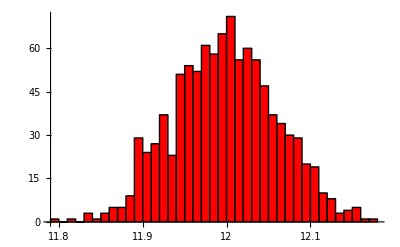

```mathematica
Histogram[means]
```

```mathematica
Sort[means]
```

```mathematica
means=Table[Mean[RandomArray[NormalDistribution[12,0.2],100]],
{i,1,1000}];
```

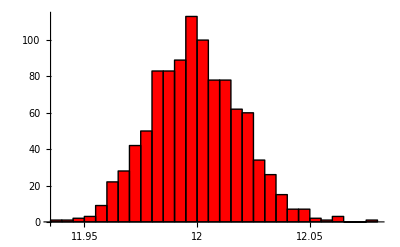

```mathematica
Histogram[means]
```

```mathematica
sds=Table[StandardDeviation[RandomArray[NormalDistribution[12,0.2],
10]],{i,1,1000}];
```

```mathematica
Histogram[sds]
```

```mathematica
Sort[sds]
```

```mathematica
Solve[(9 s^2)/0.2^2==16.92, s]
```

```mathematica
tmeans=Table[Mean[RandomArray[ExponentialDistribution[5],
1]],{i,1,1000}];
```

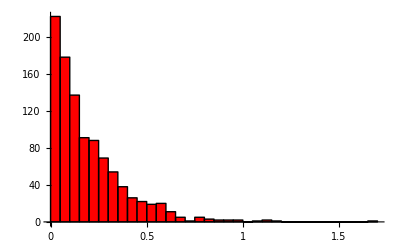

```mathematica
Histogram[tmeans]
```

```mathematica
tmeans=Table[Mean[RandomArray[ExponentialDistribution[5],
10]],{i,1,1000}];
```

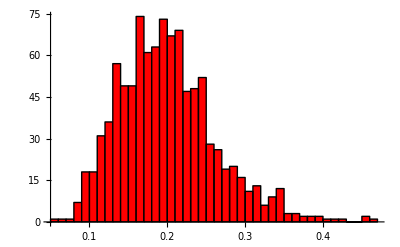

```mathematica
Histogram[tmeans]
```

```mathematica
tmeans=Table[Mean[RandomArray[ExponentialDistribution[5],
30]],{i,1,1000}];
```

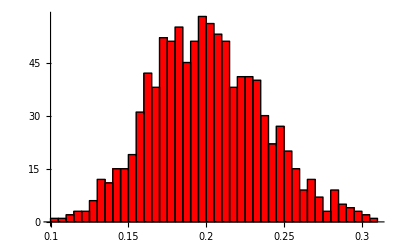

```mathematica
Histogram[tmeans]
```

```mathematica
tmeans=Table[Mean[RandomArray[ExponentialDistribution[5],
100]],{i,1,1000}];
```

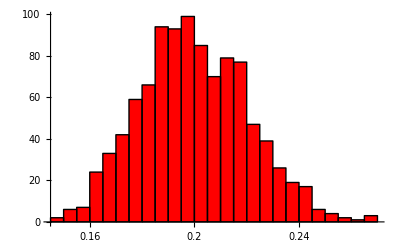

```mathematica
Histogram[tmeans]
```

#### Initialization Cells

```mathematica
Deal::usage = "Deal[n] displays the result of a deal of n cards from a standard deck."; 

RemovedCards::usage = "RemovedCards is an option to Deal that removes cards from the deck. It should be a list of 4 lists (or 4m lists if m decks are used) that indicate which clubs, diamonds, hearts, and spades are to be removed. The suit order is ♣, ◆, ♡, ♠, ♣, ◆, ♡, ♠, ♣, and so on";
 
ArrayWidth::usage = "ArrayWidth is an option to deal that specifies the number of columns in the array of cards.";

MultipleDecks::usage = "MultipleDecks is an option to Deal that, when set to an integer m, causes m multiple decks to be used.";
  


randomSet[n_Integer, k_Integer] := 
   Module[{s = Range[n], i, x}, Table[x = Random[Integer, {1, i}]; 
      {s[[i]], s[[x]]} = {s[[x]], s[[i]]}; s[[i]], {i, n, n - k + 1, -1}]]; 

randomSet[n_List, k_Integer] := n[[randomSet[Length[n], k]]]; 

 


lines = {Line[{{0, 0}, {1, 0}, {1, 1.6}, {0, 1.6}, {0, 0}}], Line[{{0, 0.8}, {1, 0.8}}]}; 

suits = {club, diamond, heart, spade};

card[s_, n_,fs_] :=Module[{nn = Mod[n,52] /. 0 -> 52},
  Graphics[{
   Text[

Style[Which[n <= 10, ToString[n], nn == 11, "J", nn == 12, "Q", nn == 13, "K"],{FontFamily -> "Times", FontWeight -> "Bold", FontSize-> fs, FontColor -> RGBColor[If[2 <= s <= 3, 1, 0], 0, 0]}],

 {0.5, 1.1}], lines, 
     RGBColor[If[2 <= s <= 3, 1, 0], 0, 0], Polygon[suits[[s]]]}, PlotRange -> All, 
    AspectRatio -> Automatic]];



Bernstein[i_, n_] := Binomial[n, i]*t^i*(1 - t)^(n - i)

Bernstein[n_] := Table[Bernstein[i, n], {i, 0, n}]

Bezier[pts_] := Bernstein[Length[pts] - 1] . pts

Options[BezierCurve] = {ShowPoints -> False}; 

BezierCurve[pts_, opts___] := 
  Module[{showpoints = ShowPoints /. {opts} /. Options[BezierCurve]}, 
   ParametricPlot[Evaluate[Bezier[pts]], {t, 0, 1}, PlotStyle -> AbsolutePointSize[1], 
    PlotRange -> All, PlotPoints -> 5,  DisplayFunction -> Identity, 
    Epilog -> If[showpoints, {AbsolutePointSize[8], Point /@ pts}, {}]]]
rawHeart = BezierCurve[0.8*{{0, -0.509529}, {-0.266669, -0.242858}, 
      {-0.31428898, 0.0904771}, {-0.152381, 0.242858}, {-0.02, 0.0619054}, 
      {0, -0.00476195}}];

rawClub1 = 
   BezierCurve[p1 = {{-0.144185, -0.830241}, {-0.0697654, -0.58837898}, 
      {-0.0372070, -0.253492}}, ShowPoints -> True]; 
rawClub2 = BezierCurve[p2 = 
     {{-0.0418583, -0.239538}, {-0.167440, -0.411633}, 
      {-0.386047, -0.52791298}, {-0.600002, -0.309306}, 
      {-0.604654, 0.0953482}, {-0.423256, 0.258140}, 
      {-0.218603, 0.22093098}, {-0.0837191, 0.132557}}, 
    ShowPoints -> True];
rawClub3 = 
   BezierCurve[p3 = {{-0.0837191, 0.127906}, 
      {-0.232557, 0.24418698}, {-0.404652, 0.416281}, 
      {-0.418605, 0.625586}, {-0.223255, 0.74651698}, 
      {-0.0744168, 0.769772}, {-0.0046486398, 0.774425}}, ShowPoints -> True]; 
rawDiamond = BezierCurve[pp = 
     {{0.0010616498, -0.226760}, {-0.0286658, -0.12025298}, 
      {-0.0583933, -0.044667598}, {-0.0987377, -(3.26218/10^6)}}]; 
rawSpade1 = BezierCurve[p1 = 
     {{-0.144185, -0.830241}, {-0.0697654, -0.58837898}, 
      {-0.0372070, -0.253492}}, ShowPoints -> True]; 
rawSpade2 = BezierCurve[p2 = 
     {{-0.0604631, -0.239538}, {-0.232557, -0.444191}, 
      {-0.497677, -0.430238}, {-0.711631, -0.155817}, {-0.637213, 0.160464}, 
      {-0.423256, 0.46279398}, {-0.148835, 0.630237}, 
      {-0.0558119, 0.75582}, {2.56673/10^6, 0.853495}}, ShowPoints -> True]; 
      
fix[suit_] := Cases[Normal[suit],Line[z_] :> z, ∞][[1]];

club = (temp = 0.3*Join[Cases[Normal[rawClub1[[1]]],Line[z_] :> z, ∞][[1]],Cases[Normal[ rawClub2[[1]]], Line[z_] :> z, ∞][[1]],Cases[Normal[ rawClub3[[1]]], Line[z_] :> z, ∞][[1]]]; 
     ({0.5, 0.35} + #1 & ) /@ Join[temp, Reverse[({-1, 1}*#1 & ) /@ temp]]); 
     
diamond = ({0.5, 0.4} + #1 & ) /@ 
    (1.3*Join[fix@rawDiamond, 
       ss = Reverse[({1, -1}*#1 & ) /@ 
        fix@ rawDiamond],  -fix@rawDiamond, -ss]);
 
heart = ({0.5, 0.55} + #1 & ) /@ 
  Join[rawHeart//fix, ({-1, 1}*#1 & ) /@ fix[rawHeart]]; 

spade = (temp = 0.3*Join[fix@rawSpade1, fix@rawSpade2]; 
     ({0.5, 0.35} + #1 & ) /@ Join[temp, Reverse[({-1, 1}*#1 & ) /@ temp]]); 

Options[Deal] = {RemovedCards -> None, ArrayWidth -> 5,
ColorCount->False, MultipleDecks->1, FontSize->16};
 

Deal[n_, opts___] := Module[{rem, m},
  {rem, aw,ccQ,m,fs} = {RemovedCards, ArrayWidth, 
  ColorCount,MultipleDecks, FontSize} /.{opts} /. Options[Deal]; 
  m = m /. False|None :> 1;
  rem = rem /. None -> {{},{},{},{}};
  cc = Complement[Range[m 52], 
    Join @@(Range[0,52 m - 13,13] + rem)]; 
  rr = Mod[randomSet[cc,n],52] /. 0 -> 52;
  Show[GraphicsArray[
    Partition[Join[(card[Quotient[# - 1, 13] + 1,
      Mod[#, 13] /. 0 -> 13,fs] &) /@ 
        rr, Table[Graphics[{}],
       {aw - Mod[n, aw] /. aw -> 0}]], aw], 
   Sequence@@FilterRules[{opts}, First /@ Options [GraphicsArray]],
   Sequence@@FilterRules[{opts}, First /@ Options [Graphics]],
   GraphicsSpacing -> 0.4,
   PlotLabel -> If[ccQ,StringForm["`` red; `` black",
    co = Count[rr, _?(13 < # < 40 &)],n-co], None],
   BaseStyle -> {FontWeight->"Bold", FontSize->fs, FontFamily->"Times"}]]]
```

Set::write: Tag BezierCurve in Options[BezierCurve] is Protected.

SetDelayed::write: Tag BezierCurve in BezierCurve[pts_, opts___] is Protected.

$Failed

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Join::heads: Heads Times and List at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

Thread::tdlen: Objects of unequal length in {1, -1}\ {} cannot be combined.

Thread::tdlen: Objects of unequal length in {}\ {1, -1} cannot be combined.

Thread::tdlen: Objects of unequal length in {1, -1}\ {} cannot be combined.

General::stop: Further output of Thread :: tdlen will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Join::heads: Heads Part and Times at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

Thread::tdlen: Objects of unequal length in {-1, 1}\ {} cannot be combined.

Join::heads: Heads Part and Times at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Join::heads: Heads Times and List at positions 1 and 2 are expected to be the same.

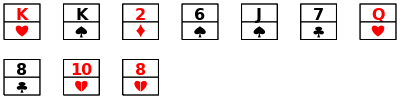

```mathematica
Deal[10,ImageSize->400, ArrayWidth->7]
```

```mathematica
{RemovedCards -> None, ArrayWidth -> 5,
ColorCount->False, MultipleDecks->1, FontSize->16};
```